# David Meretzky 785 Homework 1 FEM

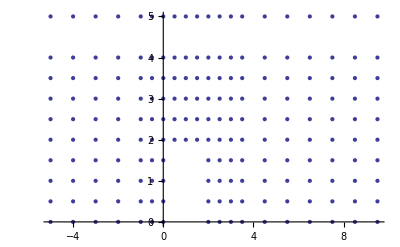

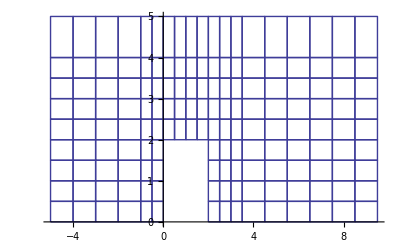

((-x+γ) (-y+δ))/((-α+γ) (-β+δ))

((x-α) (-y+δ))/((-α+γ) (-β+δ))

((x-α) (y-β))/((-α+γ) (-β+δ))

((y-β) (-x+γ))/((-α+γ) (-β+δ))

```mathematica
nodes = Import["/Users/David/Downloads/ChnlNodes.dat"];
elements = Import["/Users/David/Downloads/ChnlElems.dat"];

el= {};
For[i = 1, i ≤  155, i++,
node = nodes[[elements[[i,2;;5]],2;;3]];
 AppendTo[node,nodes[[elements[[i,2;;5]],2;;3]][[1]]];
AppendTo[el,node];
];

ListPlot[nodes[[1;;188,2;;3]]]
ListLinePlot[el, PlotStyle->Hue[.67, .6, .6]]

n1[α_,β_,γ_,δ_,x_,y_] = (((γ - x)*(δ - y))/((γ - α)*(δ-β)));
n2[α_,β_,γ_,δ_,x_,y_] = (((x - α)*(δ - y))/((γ - α)*(δ-β)));
n3[α_,β_,γ_,δ_,x_,y_] = (((x - α)*(y - β))/((γ - α)*(δ-β)));n4[α_,β_,γ_,δ_,x_,y_] = (((γ - x)*(y - β))/((γ - α)*(δ-β)));


Print[n1[α,β,γ,δ,x,y]];
Print[n2[α,β,γ,δ,x,y]];
Print[n3[α,β,γ,δ,x,y]];
Print[n4[α,β,γ,δ,x,y]];

(*For[i = 1, i ≤ 155, ++i, 
element = elements[[i]];
α = nodes[[element[[2;;5]]]][[1]][[2]];
β = nodes[[element[[2;;5]]]][[1]][[3]];
γ = nodes[[element[[2;;5]]]][[3]][[1]];
δ = nodes[[element[[2;;5]]]][[3]][[2]];
Print[n1[α,β,γ,δ,x,y]];
Print[n2[α,β,γ,δ,x,y]];
Print[n3[α,β,γ,δ,x,y]];
Print[n4[α,β,γ,δ,x,y]];
];*)
```

```mathematica
For[i = 1, i ≤ 155, ++i, 
Print[i];
element = elements[[i]];
α = nodes[[element[[2;;5]]]][[1]][[2]];
β = nodes[[element[[2;;5]]]][[1]][[3]];
γ = nodes[[element[[2;;5]]]][[3]][[1]];
δ = nodes[[element[[2;;5]]]][[3]][[2]];
Print[n1[α,β,γ,δ,x,y]];
Print[n2[α,β,γ,δ,x,y]];
Print[n3[α,β,γ,δ,x,y]];
Print[n4[α,β,γ,δ,x,y]];
];
```

1

-0.0147059 (12-x) (-4.-y)

-0.0147059 (5+x) (-4.-y)

-0.0147059 (5+x) y

-0.0147059 (12-x) y

2

-0.0123457 (13-x) (-4.-y)

-0.0123457 (5+x) (-4.-y)

-0.0123457 (5+x) (-0.5+y)

-0.0123457 (13-x) (-0.5+y)

3

-0.0105263 (14-x) (-4.-y)

-0.0105263 (5+x) (-4.-y)

-0.0105263 (5+x) (-1.+y)

-0.0105263 (14-x) (-1.+y)

4

-0.00909091 (15-x) (-4.-y)

-0.00909091 (5+x) (-4.-y)

-0.00909091 (5+x) (-1.5+y)

-0.00909091 (15-x) (-1.5+y)

5

-0.00793651 (16-x) (-4.-y)

-0.00793651 (5+x) (-4.-y)

-0.00793651 (5+x) (-2.+y)

-0.00793651 (16-x) (-2.+y)

6

-0.00699301 (17-x) (-4.-y)

-0.00699301 (5+x) (-4.-y)

-0.00699301 (5+x) (-2.5+y)

-0.00699301 (17-x) (-2.5+y)

7

-0.00621118 (18-x) (-4.-y)

-0.00621118 (5+x) (-4.-y)

-0.00621118 (5+x) (-3.+y)

-0.00621118 (18-x) (-3.+y)

8

-0.00555556 (19-x) (-4.-y)

-0.00555556 (5+x) (-4.-y)

-0.00555556 (5+x) (-3.5+y)

-0.00555556 (19-x) (-3.5+y)

9

-0.005 (20-x) (-4.-y)

-0.005 (5+x) (-4.-y)

-0.005 (5+x) (-4.+y)

-0.005 (20-x) (-4.+y)

10

-0.0128205 (22-x) (-3.-y)

-0.0128205 (4.+x) (-3.-y)

-0.0128205 (4.+x) y

-0.0128205 (22-x) y

11

-0.010582 (23-x) (-3.-y)

-0.010582 (4.+x) (-3.-y)

-0.010582 (4.+x) (-0.5+y)

-0.010582 (23-x) (-0.5+y)

12

-0.00892857 (24-x) (-3.-y)

-0.00892857 (4.+x) (-3.-y)

-0.00892857 (4.+x) (-1.+y)

-0.00892857 (24-x) (-1.+y)

13

-0.00766284 (25-x) (-3.-y)

-0.00766284 (4.+x) (-3.-y)

-0.00766284 (4.+x) (-1.5+y)

-0.00766284 (25-x) (-1.5+y)

14

-0.00666667 (26-x) (-3.-y)

-0.00666667 (4.+x) (-3.-y)

-0.00666667 (4.+x) (-2.+y)

-0.00666667 (26-x) (-2.+y)

15

-0.0058651 (27-x) (-3.-y)

-0.0058651 (4.+x) (-3.-y)

-0.0058651 (4.+x) (-2.5+y)

-0.0058651 (27-x) (-2.5+y)

16

-0.00520833 (28-x) (-3.-y)

-0.00520833 (4.+x) (-3.-y)

-0.00520833 (4.+x) (-3.+y)

-0.00520833 (28-x) (-3.+y)

17

-0.004662 (29-x) (-3.-y)

-0.004662 (4.+x) (-3.-y)

-0.004662 (4.+x) (-3.5+y)

-0.004662 (29-x) (-3.5+y)

18

-0.00420168 (30-x) (-3.-y)

-0.00420168 (4.+x) (-3.-y)

-0.00420168 (4.+x) (-4.+y)

-0.00420168 (30-x) (-4.+y)

19

-0.0142857 (32-x) (-2.-y)

-0.0142857 (3.+x) (-2.-y)

-0.0142857 (3.+x) y

-0.0142857 (32-x) y

20

-0.0111111 (33-x) (-2.-y)

-0.0111111 (3.+x) (-2.-y)

-0.0111111 (3.+x) (-0.5+y)

-0.0111111 (33-x) (-0.5+y)

21

-0.00900901 (34-x) (-2.-y)

-0.00900901 (3.+x) (-2.-y)

-0.00900901 (3.+x) (-1.+y)

-0.00900901 (34-x) (-1.+y)

22

-0.0075188 (35-x) (-2.-y)

-0.0075188 (3.+x) (-2.-y)

-0.0075188 (3.+x) (-1.5+y)

-0.0075188 (35-x) (-1.5+y)

23

-0.00641026 (36-x) (-2.-y)

-0.00641026 (3.+x) (-2.-y)

-0.00641026 (3.+x) (-2.+y)

-0.00641026 (36-x) (-2.+y)

24

-0.00555556 (37-x) (-2.-y)

-0.00555556 (3.+x) (-2.-y)

-0.00555556 (3.+x) (-2.5+y)

-0.00555556 (37-x) (-2.5+y)

25

-0.00487805 (38-x) (-2.-y)

-0.00487805 (3.+x) (-2.-y)

-0.00487805 (3.+x) (-3.+y)

-0.00487805 (38-x) (-3.+y)

26

-0.004329 (39-x) (-2.-y)

-0.004329 (3.+x) (-2.-y)

-0.004329 (3.+x) (-3.5+y)

-0.004329 (39-x) (-3.5+y)

27

-0.00387597 (40-x) (-2.-y)

-0.00387597 (3.+x) (-2.-y)

-0.00387597 (3.+x) (-4.+y)

-0.00387597 (40-x) (-4.+y)

28

-0.0227273 (42-x) (-1.-y)

-0.0227273 (2.+x) (-1.-y)

-0.0227273 (2.+x) y

-0.0227273 (42-x) y

29

-0.0148148 (43-x) (-1.-y)

-0.0148148 (2.+x) (-1.-y)

-0.0148148 (2.+x) (-0.5+y)

-0.0148148 (43-x) (-0.5+y)

30

-0.0108696 (44-x) (-1.-y)

-0.0108696 (2.+x) (-1.-y)

-0.0108696 (2.+x) (-1.+y)

-0.0108696 (44-x) (-1.+y)

31

-0.00851064 (45-x) (-1.-y)

-0.00851064 (2.+x) (-1.-y)

-0.00851064 (2.+x) (-1.5+y)

-0.00851064 (45-x) (-1.5+y)

32

-0.00694444 (46-x) (-1.-y)

-0.00694444 (2.+x) (-1.-y)

-0.00694444 (2.+x) (-2.+y)

-0.00694444 (46-x) (-2.+y)

33

-0.0058309 (47-x) (-1.-y)

-0.0058309 (2.+x) (-1.-y)

-0.0058309 (2.+x) (-2.5+y)

-0.0058309 (47-x) (-2.5+y)

34

-0.005 (48-x) (-1.-y)

-0.005 (2.+x) (-1.-y)

-0.005 (2.+x) (-3.+y)

-0.005 (48-x) (-3.+y)

35

-0.0043573 (49-x) (-1.-y)

-0.0043573 (2.+x) (-1.-y)

-0.0043573 (2.+x) (-3.5+y)

-0.0043573 (49-x) (-3.5+y)

36

-0.00384615 (50-x) (-1.-y)

-0.00384615 (2.+x) (-1.-y)

-0.00384615 (2.+x) (-4.+y)

-0.00384615 (50-x) (-4.+y)

37

-0.0377358 (52-x) (-0.5-y)

-0.0377358 (1.+x) (-0.5-y)

-0.0377358 (1.+x) y

-0.0377358 (52-x) y

38

-0.0185185 (53-x) (-0.5-y)

-0.0185185 (1.+x) (-0.5-y)

-0.0185185 (1.+x) (-0.5+y)

-0.0185185 (53-x) (-0.5+y)

39

-0.0121212 (54-x) (-0.5-y)

-0.0121212 (1.+x) (-0.5-y)

-0.0121212 (1.+x) (-1.+y)

-0.0121212 (54-x) (-1.+y)

40

-0.00892857 (55-x) (-0.5-y)

-0.00892857 (1.+x) (-0.5-y)

-0.00892857 (1.+x) (-1.5+y)

-0.00892857 (55-x) (-1.5+y)

41

-0.00701754 (56-x) (-0.5-y)

-0.00701754 (1.+x) (-0.5-y)

-0.00701754 (1.+x) (-2.+y)

-0.00701754 (56-x) (-2.+y)

42

-0.00574713 (57-x) (-0.5-y)

-0.00574713 (1.+x) (-0.5-y)

-0.00574713 (1.+x) (-2.5+y)

-0.00574713 (57-x) (-2.5+y)

43

-0.00484262 (58-x) (-0.5-y)

-0.00484262 (1.+x) (-0.5-y)

-0.00484262 (1.+x) (-3.+y)

-0.00484262 (58-x) (-3.+y)

44

-0.00416667 (59-x) (-0.5-y)

-0.00416667 (1.+x) (-0.5-y)

-0.00416667 (1.+x) (-3.5+y)

-0.00416667 (59-x) (-3.5+y)

45

-0.00364299 (60-x) (-0.5-y)

-0.00364299 (1.+x) (-0.5-y)

-0.00364299 (1.+x) (-4.+y)

-0.00364299 (60-x) (-4.+y)

46

Power::infy: Infinite expression 1/0. encountered.

ComplexInfinity

Power::infy: Infinite expression 1/0. encountered.

ComplexInfinity

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

ComplexInfinity

ComplexInfinity

47

-0.0314961 (63-x) (0.-y)

-0.0314961 (0.5+x) (0.-y)

-0.0314961 (0.5+x) (-0.5+y)

-0.0314961 (63-x) (-0.5+y)

48

-0.0155039 (64-x) (0.-y)

-0.0155039 (0.5+x) (0.-y)

-0.0155039 (0.5+x) (-1.+y)

-0.0155039 (64-x) (-1.+y)

49

-0.0101781 (65-x) (0.-y)

-0.0101781 (0.5+x) (0.-y)

-0.0101781 (0.5+x) (-1.5+y)

-0.0101781 (65-x) (-1.5+y)

50

-0.0075188 (66-x) (0.-y)

-0.0075188 (0.5+x) (0.-y)

-0.0075188 (0.5+x) (-2.+y)

-0.0075188 (66-x) (-2.+y)

51

-0.00592593 (67-x) (0.-y)

-0.00592593 (0.5+x) (0.-y)

-0.00592593 (0.5+x) (-2.5+y)

-0.00592593 (67-x) (-2.5+y)

52

-0.00486618 (68-x) (0.-y)

-0.00486618 (0.5+x) (0.-y)

-0.00486618 (0.5+x) (-3.+y)

-0.00486618 (68-x) (-3.+y)

53

-0.004111 (69-x) (0.-y)

-0.004111 (0.5+x) (0.-y)

-0.004111 (0.5+x) (-3.5+y)

-0.004111 (69-x) (-3.5+y)

54

-0.0035461 (70-x) (0.-y)

-0.0035461 (0.5+x) (0.-y)

-0.0035461 (0.5+x) (-4.+y)

-0.0035461 (70-x) (-4.+y)

55

-0.00925926 (72-x) (0.5-y)

-0.00925926 (0.+x) (0.5-y)

-0.00925926 (0.+x) (-2.+y)

-0.00925926 (72-x) (-2.+y)

56

-0.00684932 (73-x) (0.5-y)

-0.00684932 (0.+x) (0.5-y)

-0.00684932 (0.+x) (-2.5+y)

-0.00684932 (73-x) (-2.5+y)

57

-0.00540541 (74-x) (0.5-y)

-0.00540541 (0.+x) (0.5-y)

-0.00540541 (0.+x) (-3.+y)

-0.00540541 (74-x) (-3.+y)

58

-0.00444444 (75-x) (0.5-y)

-0.00444444 (0.+x) (0.5-y)

-0.00444444 (0.+x) (-3.5+y)

-0.00444444 (75-x) (-3.5+y)

59

-0.0037594 (76-x) (0.5-y)

-0.0037594 (0.+x) (0.5-y)

-0.0037594 (0.+x) (-4.+y)

-0.0037594 (76-x) (-4.+y)

60

-0.0129032 (78-x) (1.-y)

-0.0129032 (-0.5+x) (1.-y)

-0.0129032 (-0.5+x) (-2.+y)

-0.0129032 (78-x) (-2.+y)

61

-0.00849257 (79-x) (1.-y)

-0.00849257 (-0.5+x) (1.-y)

-0.00849257 (-0.5+x) (-2.5+y)

-0.00849257 (79-x) (-2.5+y)

62

-0.00628931 (80-x) (1.-y)

-0.00628931 (-0.5+x) (1.-y)

-0.00628931 (-0.5+x) (-3.+y)

-0.00628931 (80-x) (-3.+y)

63

-0.00496894 (81-x) (1.-y)

-0.00496894 (-0.5+x) (1.-y)

-0.00496894 (-0.5+x) (-3.5+y)

-0.00496894 (81-x) (-3.5+y)

64

-0.00408998 (82-x) (1.-y)

-0.00408998 (-0.5+x) (1.-y)

-0.00408998 (-0.5+x) (-4.+y)

-0.00408998 (82-x) (-4.+y)

65

-0.0240964 (84-x) (1.5-y)

-0.0240964 (-1.+x) (1.5-y)

-0.0240964 (-1.+x) (-2.+y)

-0.0240964 (84-x) (-2.+y)

66

-0.0119048 (85-x) (1.5-y)

-0.0119048 (-1.+x) (1.5-y)

-0.0119048 (-1.+x) (-2.5+y)

-0.0119048 (85-x) (-2.5+y)

67

-0.00784314 (86-x) (1.5-y)

-0.00784314 (-1.+x) (1.5-y)

-0.00784314 (-1.+x) (-3.+y)

-0.00784314 (86-x) (-3.+y)

68

-0.00581395 (87-x) (1.5-y)

-0.00581395 (-1.+x) (1.5-y)

-0.00581395 (-1.+x) (-3.5+y)

-0.00581395 (87-x) (-3.5+y)

69

-0.0045977 (88-x) (1.5-y)

-0.0045977 (-1.+x) (1.5-y)

-0.0045977 (-1.+x) (-4.+y)

-0.0045977 (88-x) (-4.+y)

70

ComplexInfinity

ComplexInfinity

ComplexInfinity

«1 more identical outputs»

71

-0.0213904 (95-x) (2.-y)

-0.0213904 (-1.5+x) (2.-y)

-0.0213904 (-1.5+x) (-2.5+y)

-0.0213904 (95-x) (-2.5+y)

72

-0.010582 (96-x) (2.-y)

-0.010582 (-1.5+x) (2.-y)

-0.010582 (-1.5+x) (-3.+y)

-0.010582 (96-x) (-3.+y)

73

-0.0069808 (97-x) (2.-y)

-0.0069808 (-1.5+x) (2.-y)

-0.0069808 (-1.5+x) (-3.5+y)

-0.0069808 (97-x) (-3.5+y)

74

-0.00518135 (98-x) (2.-y)

-0.00518135 (-1.5+x) (2.-y)

-0.00518135 (-1.5+x) (-4.+y)

-0.00518135 (98-x) (-4.+y)

75

0.00408163 (100-x) (2.5-y)

0.00408163 (-2.+x) (2.5-y)

0.00408163 (-2.+x) y

0.00408163 (100-x) y

76

0.00505051 (101-x) (2.5-y)

0.00505051 (-2.+x) (2.5-y)

0.00505051 (-2.+x) (-0.5+y)

0.00505051 (101-x) (-0.5+y)

77

0.00666667 (102-x) (2.5-y)

0.00666667 (-2.+x) (2.5-y)

0.00666667 (-2.+x) (-1.+y)

0.00666667 (102-x) (-1.+y)

78

0.00990099 (103-x) (2.5-y)

0.00990099 (-2.+x) (2.5-y)

0.00990099 (-2.+x) (-1.5+y)

0.00990099 (103-x) (-1.5+y)

79

0.0196078 (104-x) (2.5-y)

0.0196078 (-2.+x) (2.5-y)

0.0196078 (-2.+x) (-2.+y)

0.0196078 (104-x) (-2.+y)

80

ComplexInfinity

ComplexInfinity

ComplexInfinity

«1 more identical outputs»

81

-0.0192308 (106-x) (2.5-y)

-0.0192308 (-2.+x) (2.5-y)

-0.0192308 (-2.+x) (-3.+y)

-0.0192308 (106-x) (-3.+y)

82

-0.00952381 (107-x) (2.5-y)

-0.00952381 (-2.+x) (2.5-y)

-0.00952381 (-2.+x) (-3.5+y)

-0.00952381 (107-x) (-3.5+y)

83

-0.00628931 (108-x) (2.5-y)

-0.00628931 (-2.+x) (2.5-y)

-0.00628931 (-2.+x) (-4.+y)

-0.00628931 (108-x) (-4.+y)

84

0.00310078 (110-x) (3.-y)

0.00310078 (-2.5+x) (3.-y)

0.00310078 (-2.5+x) y

0.00310078 (110-x) y

85

0.00368664 (111-x) (3.-y)

0.00368664 (-2.5+x) (3.-y)

0.00368664 (-2.5+x) (-0.5+y)

0.00368664 (111-x) (-0.5+y)

86

0.00456621 (112-x) (3.-y)

0.00456621 (-2.5+x) (3.-y)

0.00456621 (-2.5+x) (-1.+y)

0.00456621 (112-x) (-1.+y)

87

0.00603318 (113-x) (3.-y)

0.00603318 (-2.5+x) (3.-y)

0.00603318 (-2.5+x) (-1.5+y)

0.00603318 (113-x) (-1.5+y)

88

0.00896861 (114-x) (3.-y)

0.00896861 (-2.5+x) (3.-y)

0.00896861 (-2.5+x) (-2.+y)

0.00896861 (114-x) (-2.+y)

89

0.0177778 (115-x) (3.-y)

0.0177778 (-2.5+x) (3.-y)

0.0177778 (-2.5+x) (-2.5+y)

0.0177778 (115-x) (-2.5+y)

90

ComplexInfinity

ComplexInfinity

ComplexInfinity

«1 more identical outputs»

91

-0.0174672 (117-x) (3.-y)

-0.0174672 (-2.5+x) (3.-y)

-0.0174672 (-2.5+x) (-3.5+y)

-0.0174672 (117-x) (-3.5+y)

92

-0.00865801 (118-x) (3.-y)

-0.00865801 (-2.5+x) (3.-y)

-0.00865801 (-2.5+x) (-4.+y)

-0.00865801 (118-x) (-4.+y)

93

0.002442 (120-x) (3.5-y)

0.002442 (-3.+x) (3.5-y)

0.002442 (-3.+x) y

0.002442 (120-x) y

94

0.00282486 (121-x) (3.5-y)

0.00282486 (-3.+x) (3.5-y)

0.00282486 (-3.+x) (-0.5+y)

0.00282486 (121-x) (-0.5+y)

95

0.00336134 (122-x) (3.5-y)

0.00336134 (-3.+x) (3.5-y)

0.00336134 (-3.+x) (-1.+y)

0.00336134 (122-x) (-1.+y)

96

0.00416667 (123-x) (3.5-y)

0.00416667 (-3.+x) (3.5-y)

0.00416667 (-3.+x) (-1.5+y)

0.00416667 (123-x) (-1.5+y)

97

0.00550964 (124-x) (3.5-y)

0.00550964 (-3.+x) (3.5-y)

0.00550964 (-3.+x) (-2.+y)

0.00550964 (124-x) (-2.+y)

98

0.00819672 (125-x) (3.5-y)

0.00819672 (-3.+x) (3.5-y)

0.00819672 (-3.+x) (-2.5+y)

0.00819672 (125-x) (-2.5+y)

99

0.0162602 (126-x) (3.5-y)

0.0162602 (-3.+x) (3.5-y)

0.0162602 (-3.+x) (-3.+y)

0.0162602 (126-x) (-3.+y)

100

ComplexInfinity

ComplexInfinity

ComplexInfinity

«1 more identical outputs»

101

-0.016 (128-x) (3.5-y)

-0.016 (-3.+x) (3.5-y)

-0.016 (-3.+x) (-4.+y)

-0.016 (128-x) (-4.+y)

102

0.0017567 (130-x) (4.5-y)

0.0017567 (-3.5+x) (4.5-y)

0.0017567 (-3.5+x) y

0.0017567 (130-x) y

103

0.00196078 (131-x) (4.5-y)

0.00196078 (-3.5+x) (4.5-y)

0.00196078 (-3.5+x) (-0.5+y)

0.00196078 (131-x) (-0.5+y)

104

0.00222346 (132-x) (4.5-y)

0.00222346 (-3.5+x) (4.5-y)

0.00222346 (-3.5+x) (-1.+y)

0.00222346 (132-x) (-1.+y)

105

0.002574 (133-x) (4.5-y)

0.002574 (-3.5+x) (4.5-y)

0.002574 (-3.5+x) (-1.5+y)

0.002574 (133-x) (-1.5+y)

106

0.00306513 (134-x) (4.5-y)

0.00306513 (-3.5+x) (4.5-y)

0.00306513 (-3.5+x) (-2.+y)

0.00306513 (134-x) (-2.+y)

107

0.00380228 (135-x) (4.5-y)

0.00380228 (-3.5+x) (4.5-y)

0.00380228 (-3.5+x) (-2.5+y)

0.00380228 (135-x) (-2.5+y)

108

0.00503145 (136-x) (4.5-y)

0.00503145 (-3.5+x) (4.5-y)

0.00503145 (-3.5+x) (-3.+y)

0.00503145 (136-x) (-3.+y)

109

0.00749064 (137-x) (4.5-y)

0.00749064 (-3.5+x) (4.5-y)

0.00749064 (-3.5+x) (-3.5+y)

0.00749064 (137-x) (-3.5+y)

110

0.0148699 (138-x) (4.5-y)

0.0148699 (-3.5+x) (4.5-y)

0.0148699 (-3.5+x) (-4.+y)

0.0148699 (138-x) (-4.+y)

111

0.00134183 (140-x) (5.5-y)

0.00134183 (-4.5+x) (5.5-y)

0.00134183 (-4.5+x) y

0.00134183 (140-x) y

112

0.0014652 (141-x) (5.5-y)

0.0014652 (-4.5+x) (5.5-y)

0.0014652 (-4.5+x) (-0.5+y)

0.0014652 (141-x) (-0.5+y)

113

0.00161616 (142-x) (5.5-y)

0.00161616 (-4.5+x) (5.5-y)

0.00161616 (-4.5+x) (-1.+y)

0.00161616 (142-x) (-1.+y)

114

0.00180505 (143-x) (5.5-y)

0.00180505 (-4.5+x) (5.5-y)

0.00180505 (-4.5+x) (-1.5+y)

0.00180505 (143-x) (-1.5+y)

115

0.00204813 (144-x) (5.5-y)

0.00204813 (-4.5+x) (5.5-y)

0.00204813 (-4.5+x) (-2.+y)

0.00204813 (144-x) (-2.+y)

116

0.00237248 (145-x) (5.5-y)

0.00237248 (-4.5+x) (5.5-y)

0.00237248 (-4.5+x) (-2.5+y)

0.00237248 (145-x) (-2.5+y)

117

0.00282686 (146-x) (5.5-y)

0.00282686 (-4.5+x) (5.5-y)

0.00282686 (-4.5+x) (-3.+y)

0.00282686 (146-x) (-3.+y)

118

0.00350877 (147-x) (5.5-y)

0.00350877 (-4.5+x) (5.5-y)

0.00350877 (-4.5+x) (-3.5+y)

0.00350877 (147-x) (-3.5+y)

119

0.00464576 (148-x) (5.5-y)

0.00464576 (-4.5+x) (5.5-y)

0.00464576 (-4.5+x) (-4.+y)

0.00464576 (148-x) (-4.+y)

120

0.00106468 (150-x) (6.5-y)

0.00106468 (-5.5+x) (6.5-y)

0.00106468 (-5.5+x) y

0.00106468 (150-x) y

121

0.00114548 (151-x) (6.5-y)

0.00114548 (-5.5+x) (6.5-y)

0.00114548 (-5.5+x) (-0.5+y)

0.00114548 (151-x) (-0.5+y)

122

0.00124108 (152-x) (6.5-y)

0.00124108 (-5.5+x) (6.5-y)

0.00124108 (-5.5+x) (-1.+y)

0.00124108 (152-x) (-1.+y)

123

0.00135593 (153-x) (6.5-y)

0.00135593 (-5.5+x) (6.5-y)

0.00135593 (-5.5+x) (-1.5+y)

0.00135593 (153-x) (-1.5+y)

124

0.00149645 (154-x) (6.5-y)

0.00149645 (-5.5+x) (6.5-y)

0.00149645 (-5.5+x) (-2.+y)

0.00149645 (154-x) (-2.+y)

125

0.00167224 (155-x) (6.5-y)

0.00167224 (-5.5+x) (6.5-y)

0.00167224 (-5.5+x) (-2.5+y)

0.00167224 (155-x) (-2.5+y)

126

0.00189843 (156-x) (6.5-y)

0.00189843 (-5.5+x) (6.5-y)

0.00189843 (-5.5+x) (-3.+y)

0.00189843 (156-x) (-3.+y)

127

0.00220022 (157-x) (6.5-y)

0.00220022 (-5.5+x) (6.5-y)

0.00220022 (-5.5+x) (-3.5+y)

0.00220022 (157-x) (-3.5+y)

128

0.00262295 (158-x) (6.5-y)

0.00262295 (-5.5+x) (6.5-y)

0.00262295 (-5.5+x) (-4.+y)

0.00262295 (158-x) (-4.+y)

129

0.000868621 (160-x) (7.5-y)

0.000868621 (-6.5+x) (7.5-y)

0.000868621 (-6.5+x) y

0.000868621 (160-x) y

130

0.000924642 (161-x) (7.5-y)

0.000924642 (-6.5+x) (7.5-y)

0.000924642 (-6.5+x) (-0.5+y)

0.000924642 (161-x) (-0.5+y)

131

0.000989364 (162-x) (7.5-y)

0.000989364 (-6.5+x) (7.5-y)

0.000989364 (-6.5+x) (-1.+y)

0.000989364 (162-x) (-1.+y)

132

0.00106496 (163-x) (7.5-y)

0.00106496 (-6.5+x) (7.5-y)

0.00106496 (-6.5+x) (-1.5+y)

0.00106496 (163-x) (-1.5+y)

133

0.0011544 (164-x) (7.5-y)

0.0011544 (-6.5+x) (7.5-y)

0.0011544 (-6.5+x) (-2.+y)

0.0011544 (164-x) (-2.+y)

134

0.00126183 (165-x) (7.5-y)

0.00126183 (-6.5+x) (7.5-y)

0.00126183 (-6.5+x) (-2.5+y)

0.00126183 (165-x) (-2.5+y)

135

0.00139324 (166-x) (7.5-y)

0.00139324 (-6.5+x) (7.5-y)

0.00139324 (-6.5+x) (-3.+y)

0.00139324 (166-x) (-3.+y)

136

0.00155763 (167-x) (7.5-y)

0.00155763 (-6.5+x) (7.5-y)

0.00155763 (-6.5+x) (-3.5+y)

0.00155763 (167-x) (-3.5+y)

137

0.00176913 (168-x) (7.5-y)

0.00176913 (-6.5+x) (7.5-y)

0.00176913 (-6.5+x) (-4.+y)

0.00176913 (168-x) (-4.+y)

138

0.000723982 (170-x) (8.5-y)

0.000723982 (-7.5+x) (8.5-y)

0.000723982 (-7.5+x) y

0.000723982 (170-x) y

139

0.000764526 (171-x) (8.5-y)

0.000764526 (-7.5+x) (8.5-y)

0.000764526 (-7.5+x) (-0.5+y)

0.000764526 (171-x) (-0.5+y)

140

0.000810537 (172-x) (8.5-y)

0.000810537 (-7.5+x) (8.5-y)

0.000810537 (-7.5+x) (-1.+y)

0.000810537 (172-x) (-1.+y)

141

0.000863185 (173-x) (8.5-y)

0.000863185 (-7.5+x) (8.5-y)

0.000863185 (-7.5+x) (-1.5+y)

0.000863185 (173-x) (-1.5+y)

142

0.000924001 (174-x) (8.5-y)

0.000924001 (-7.5+x) (8.5-y)

0.000924001 (-7.5+x) (-2.+y)

0.000924001 (174-x) (-2.+y)

143

0.000995025 (175-x) (8.5-y)

0.000995025 (-7.5+x) (8.5-y)

0.000995025 (-7.5+x) (-2.5+y)

0.000995025 (175-x) (-2.5+y)

144

0.00107904 (176-x) (8.5-y)

0.00107904 (-7.5+x) (8.5-y)

0.00107904 (-7.5+x) (-3.+y)

0.00107904 (176-x) (-3.+y)

145

0.00117994 (177-x) (8.5-y)

0.00117994 (-7.5+x) (8.5-y)

0.00117994 (-7.5+x) (-3.5+y)

0.00117994 (177-x) (-3.5+y)

146

0.00130336 (178-x) (8.5-y)

0.00130336 (-7.5+x) (8.5-y)

0.00130336 (-7.5+x) (-4.+y)

0.00130336 (178-x) (-4.+y)

147

0.000613779 (180-x) (9.5-y)

0.000613779 (-8.5+x) (9.5-y)

0.000613779 (-8.5+x) y

0.000613779 (180-x) y

148

0.000644122 (181-x) (9.5-y)

0.000644122 (-8.5+x) (9.5-y)

0.000644122 (-8.5+x) (-0.5+y)

0.000644122 (181-x) (-0.5+y)

149

0.000678081 (182-x) (9.5-y)

0.000678081 (-8.5+x) (9.5-y)

0.000678081 (-8.5+x) (-1.+y)

0.000678081 (182-x) (-1.+y)

150

0.000716332 (183-x) (9.5-y)

0.000716332 (-8.5+x) (9.5-y)

0.000716332 (-8.5+x) (-1.5+y)

0.000716332 (183-x) (-1.5+y)

151

0.000759734 (184-x) (9.5-y)

0.000759734 (-8.5+x) (9.5-y)

0.000759734 (-8.5+x) (-2.+y)

0.000759734 (184-x) (-2.+y)

152

0.000809389 (185-x) (9.5-y)

0.000809389 (-8.5+x) (9.5-y)

0.000809389 (-8.5+x) (-2.5+y)

0.000809389 (185-x) (-2.5+y)

153

0.000866739 (186-x) (9.5-y)

0.000866739 (-8.5+x) (9.5-y)

0.000866739 (-8.5+x) (-3.+y)

0.000866739 (186-x) (-3.+y)

154

0.000933707 (187-x) (9.5-y)

0.000933707 (-8.5+x) (9.5-y)

0.000933707 (-8.5+x) (-3.5+y)

0.000933707 (187-x) (-3.5+y)

155

0.00101291 (188-x) (9.5-y)

0.00101291 (-8.5+x) (9.5-y)

0.00101291 (-8.5+x) (-4.+y)

0.00101291 (188-x) (-4.+y)

```mathematica
nodes[[elements[[100]][[2;;5]]]]
```

{{116,3.,3.5},{126,3.5,3.5},{127,3.5,4.},{117,3.,4.}}

```mathematica
element = elements[[46]];
α = nodes[[element[[2;;5]]]][[1]][[2]]
β = nodes[[element[[2;;5]]]][[1]][[3]]
γ = nodes[[element[[2;;5]]]][[3]][[1]]
δ = nodes[[element[[2;;5]]]][[3]][[2]]
Print[n1[α,β,γ,δ,x,y]];
Print[n2[α,β,γ,δ,x,y]];
Print[n3[α,β,γ,δ,x,y]];
Print[n4[α,β,γ,δ,x,y]];
```

-0.5

0

62

0.

Power::infy: Infinite expression 1/0. encountered.

ComplexInfinity

Power::infy: Infinite expression 1/0. encountered.

ComplexInfinity

Power::infy: Infinite expression 1/0. encountered.

ComplexInfinity

Power::infy: Infinite expression 1/0. encountered.

ComplexInfinity

```mathematica
nj = element[[2;;5]][[j]];
nk = element[[2;;5]][[k]];knByn[[nj,nk]] +=
```